{M→1/15625,S→1/10000000000,L→0.0011,epsi→0.01,G→0.0000116,r→1,g→61.75,mpl→2.44×10^18}

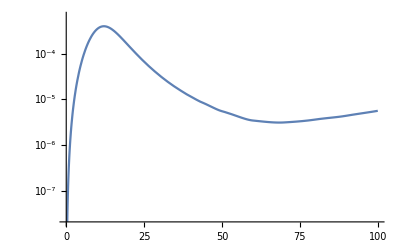

```mathematica
Parameters={M-> 64*10^-6, S-> 10^-10, L-> 1.1*10^-3, epsi-> 0.01, G-> 1.16*10^-5, r-> 1, g-> 61.75, mpl-> 2.44*10^18}
solution = NDSolve[{ f'[T] ==((-1.27*G^2*epsi*T^2*M^2*S*(45/(4*3.14)^3)^0.5*g^-0.5*mpl/4)/(M^2*S +(M*(1-S)^0.5-(2*2^0.5*1.2*G*L*T^3/3.14^2)+r*G^2*T^5)^2))(1/(E^epsi+1) - f[T]), f[10^6]== 0} /. Parameters, f , {T, 0,100}];
LogPlot[Evaluate[f[T]/. solution ]*(T^3/2*3.14^3)*(epsi^2/(E^epsi+1))/.Parameters, {T,0,100}]
```

{1/15625→1/15625,1/10000000000→1/10000000000,0.0011→1/10000,epsi→0.0001,0.0000116→0.0000116,79→79,10.75→61.75,2.44×10^18→2.44×10^18}

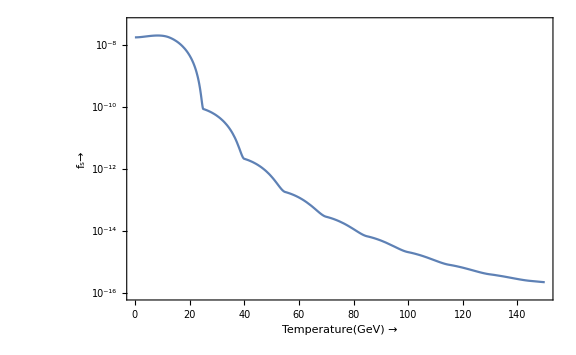

```mathematica
Parameters={M-> 64*10^-6(*GeV*) , S-> 10^-10, L-> 10^-4, epsi-> 0.0001, G-> 1.16*10^-5(*Fermi constant (GeV)*), r-> 79, g-> 61.75, mpl-> 2.44*10^18(*GeV*)}
solution = NDSolve[{ f'[T] ==((-1.27*G^2*epsi*T^2*M^2*S*(45/(4*3.14)^3)^0.5*g^-0.5*mpl/4)/(M^2*S +(M*(1-S)^0.5-(2*2^0.5*1.2*G*L*T^3/3.14^2)+r*G^2*T^5)^2))*(1/(E^epsi+1) - f[T]), f[10^6]== 0} /. Parameters, f , {T, 150,500}];
bc = Evaluate[f[150] /. solution];
solution1 = NDSolve[{ f'[T] ==((-1.27*G^2*epsi*T^2*M^2*S*(45/(4*3.14)^3)^0.5*g^-0.5*mpl/4)/(M^2*S +(M*(1-S)^0.5-(2*2^0.5*1.2*G*L*T^3/3.14^2)+r*G^2*T^5)^2))(1/(E^epsi+1) - f[T]), f[200]== bc} /. Parameters, f , {T, 0,150}];
LogPlot[Evaluate[f[T]/. solution1 ], {T,0,150},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"Temperature(GeV) →","f_s→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large]
```

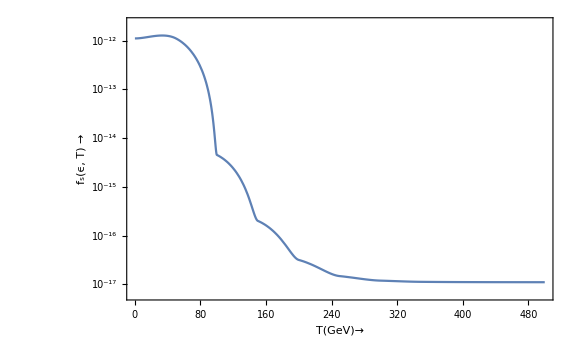

```mathematica
Parameters={M-> 64*10^-6(*GeV*) , S-> 10^-10, L-> 10^-4, epsi-> 0.0001 (*Scaled momentum(P/T)*), G-> 1.16*10^-5(*Fermi constant (GeV)*), r-> 79, g-> 61.75, mpl-> 2.44*10^18(*GeV*)};
solution = NDSolve[{ f'[T] ==((-1.27*G^2*epsi*T^2*M^2*S*(45/(4*3.14)^3)^0.5*g^-0.5*mpl/4)/(M^2*S +(M*(1-S)^0.5-(2*2^0.5*1.2*G*L*T^3/3.14^2)+r*G^2*T^5)^2))*(1/(E^epsi+1) - f[T]), f[10^6]== 0} /. Parameters, f , {T, 0,500}];
LogPlot[Evaluate[f[T]/. solution ]/.Parameters, {T,0,500},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"T(GeV)→","f_s(ϵ, T) →"},PlotStyle->Automatic, LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large]
```